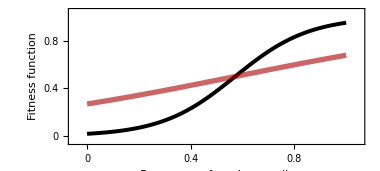

```mathematica
f1[p_,β_,α_,γ1_,γ2_,κ_,n_]:=γ1(1(*+ⅇ^α*))/(1+Exp[-(β (1+p(n-1))/n-α)])-κ;
f2[p_,β_,α_,γ1_,γ2_,n_]:=γ2(1(*+ⅇ^α*))/(1+Exp[-(β (p(n-1))/n-α)]);
Plot[
{
f2[y,8,4,1,1,8],
f2[y,2,1,1,1,8]
}
,{y,0,1}
,PlotRange->{{-0.05,1.05},{-0.05,1.05}}
,Frame->True
,ImageSize->380
,LabelStyle->{FontSize->14,Black,FontFamily->"Arial"}
,FrameStyle->Directive[Thickness[0.004],Black]
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.45
,PlotStyle->{{Thickness[0.0075],Black},{Thickness[0.01],Opacity[0.6,Darker[Red]]}}
,FrameLabel->{{"Fitness function",None},{"Frequency of producer cells",None(*"n=8, σ=β/2"*)}}
]
```

#### Limit σ to ∞

```mathematica
Limit[(1+ⅇ^σ)/(1+Exp[-(β (1+y(n-1))/n-σ)])-κ,σ->∞]

Limit[(1+ⅇ^σ)/(1+Exp[-(β (y(n-1))/n-σ)]),σ->∞]
```

ⅇ^((β+(-1+n) y β)/n)-κ

ⅇ^(((-1+n) y β)/n)

```mathematica
Manipulate[
LogPlot[
{Exp[β/n+(n-1)/n β p]-κ,Exp[(n-1)/n β p]},{p,0,1}
,PlotStyle->{Black,Red}
]
,{{n,10},1,100,1}
,{{β,2},0,100,0.1}
,{{κ,0.1},0,1,0.01}
]
```

```mathematica
Series[Exp[β/n+(n-1)/n β y]-κ,{n,∞,1}]
Series[Exp[(n-1)/n β y],{n,∞,1}]
```

(ⅇ^(y β)-κ)-(ⅇ^(y β) (-1+y) β)/n+O[1/n]^2

ⅇ^(y β)-(ⅇ^(y β) y β)/n+O[1/n]^2

#### β to ∞

```mathematica
Limit[(1+ⅇ^σ)/(1+Exp[-(β A-σ)])-κ,β->∞]

Limit[(1+ⅇ^σ)/(1+Exp[-(β B-σ)]),β->∞]
```

ConditionalExpression[1+ⅇ^σ-κ,(ⅇ^σ|σ|κ)∈ℝ&&A>0]

ConditionalExpression[1+ⅇ^σ,(ⅇ^σ|σ)∈ℝ&&B>0]

```mathematica
Solve[Log[Exp[β/n]-1]+B β==F,β]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[B β+Log[-1+ⅇ^(β/n)]==F,β]

```mathematica
Series[β/n+(n-1)/n β y,{n,∞,1}]
```

y β+(β-y β)/n+O[1/n]^2

```mathematica
Manipulate[
Plot[Log[Exp[β/n]-1]+(n-1)/n y β-Log[0.1],{β,0,5},Frame->True,PlotRange->{All,{-10,10}}]
,{{n,10},5,50,5}
,{{y,0.5},0,1,0.01}
]
```

#### Bi-stability Criteria for large σ

```mathematica
Δ[y_,n_,κ_]:=Exp[β(1/n+(n-1)/n y)]-κ-Exp[(n-1)/n y β]

Δ[0,n,κ]//FullSimplify

Δ[1,n,κ]//FullSimplify
```

-1+ⅇ^(β/n)-κ

ⅇ^β-ⅇ^(((-1+n) β)/n)-κ

```mathematica
Solve[Δ[0,n,κ]==0,β]
(*Solve[Δ[1]==0,β]*)
Solve[{ⅇ^β β/n-κ==0},β]//FullSimplify
```

{{β→ConditionalExpression[n (2 ⅈ π C[1]+Log[1+κ]),C[1]∈ℤ]}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{β→ProductLog[n κ]}}

```mathematica
25 Log[1+0.1]
```

2.38275

```mathematica
Series[Exp[n ϵ]-Exp[(n-1) ϵ],{ϵ,0,2}]
```

ϵ+(-1/2+n) ϵ^2+O[ϵ]^3

```mathematica
s[n_,κ_]:={ProductLog[n κ],n Log[1+κ]}

s[50,0.1]
```

{1.32672,4.76551}

```mathematica
Series[((-1+n) β)/n,{β,0,4}]

Series[Exp[β](1-Exp[-ϵ]),{ϵ,0,1}]

Series[Exp[-ϵ],{ϵ,0,1}]
```

(1-1/n) β+O[β]^5

ⅇ^β ϵ+O[ϵ]^2

1-ϵ+O[ϵ]^2

```mathematica
Exp[β]-Exp[β]Exp[-β/n]-Exp[β](1-Exp[-β/n])//FullSimplify
```

0